```mathematica
(*使用前加载"所有函数.nb"中的所有函数,注意修改tmpfile变量的值，即临时文件夹的位置*)
data=TTSData["拉拉拉",-4];
Sound[SampledSoundList[data,{44100,16}]]
(*让微软慧慧发声*)
```

-Graphics-

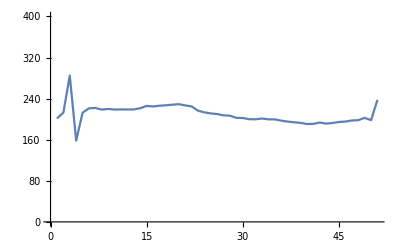

```mathematica
windowlist=Windowlist[2048,Hamming];
fdata=BaseF[Abs@Fourier@Join[windowlist#,ConstantArray[0,7*2048]]]&/@Partition[data,2048,1024];
ListLinePlot[fdata[[;;,1]],PlotRange->{{0,Length[fdata]},{0,400}}]
(*基频曲线*)
ListAnimate[Table[ListLinePlot[{44100/(8*2048)#1,#2}&@@@(fdata[[i,2]]),PlotRange->{{0,3000},{0,8}}],{i,1,Length[fdata]}]]
(*观察共振峰的变化*)
```

```mathematica
data2=FTShift[300][data];
(*变调为300Hz*)
Sound[SampledSoundList[data2,{44100,16}]]
```

-Graphics-

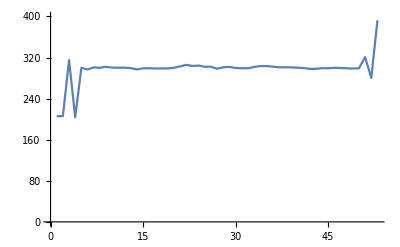

```mathematica
fdata2=BaseF[Abs@Fourier@Join[windowlist#,ConstantArray[0,7*2048]],{200,400}]&/@Partition[data2,2048,1024];
(*每帧的频谱数据*)
ListLinePlot[fdata2[[;;,1]],PlotRange->{{0,Length[fdata2]},{0,400}}]
(*基频曲线*)
ListAnimate[Table[ListLinePlot[{44100/(8*2048)#1,#2}&@@@(fdata2[[i,2]]),PlotRange->{{0,3000},{0,8}}],{i,1,Length[fdata]}]]
(*观察共振峰的变化*)
```

```mathematica
fbase=250+100#&;
(*目标频率曲线*)
tgoal=If[#<0.5,0.6#,1.4#-0.4]&;
(*时间拉伸曲线*)
data3=FTShift[fbase,tgoal][data];
Sound[SampledSoundList[data2,{44100,16}]]
```

-Graphics-

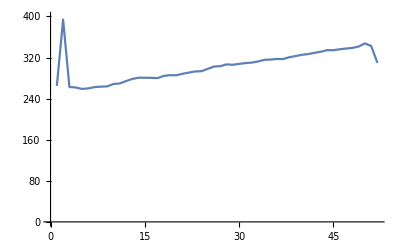

```mathematica
fdata3=BaseF[Abs@Fourier@Join[windowlist#,ConstantArray[0,7*2048]],{200,400}]&/@Partition[data3,2048,1024];
(*每帧的频谱数据*)
ListLinePlot[fdata3[[;;,1]],PlotRange->{{0,Length[fdata3]},{0,400}}]
(*基频曲线*)
ListAnimate[Table[ListLinePlot[{44100/(8*2048)#1,#2}&@@@(fdata3[[i,2]]),PlotRange->{{0,3000},{0,8}}],{i,1,Length[fdata3]}]]
```